```mathematica
<<CustomTicks`
```

```mathematica
tickll=LogTicks[-20,10];
Do[tickll[[i,1]]=10^tickll[[i,1]],{i,1,Length[tickll]}];
tickll;
```

```mathematica
mass={200,300,500,800,1000,1200,1500,1800,2000,2200,2500,2700,2900};
```

## Trident process

#### input data

```mathematica
xsmumu2mumuax={6.9*10^-9,6.87*10^-9,6.03*10^-9+2*1.08*10^-10+3.78*10^-11,4.52*10^-9+2*1.14*10^-10+5.79*10^-11,3.66*10^-9+2*1.04*10^-10+5.79*10^-11,2.93*10^-9+2*9.05*10^-11,2.06*10^-9,1.4*10^-9,1.05*10^-9,7.64*10^-10+2*2.93*10^-11+1.3*10^-11,4.23*10^-10+2*1.68*10^-11+1.3*10^-11,2.39*10^-10+2*9.69*10^-12+7.6*10^-12,7.6*10^-11+2*3.16*10^-12+2.5*10^-12}*{0.997/(2.22*10^-3),0.981/(2.2*10^-3),0.97/(2.17*10^-3),0.97/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3)}/100(*rescale fa from 1TeV to 10TeV*);
xsmumu2vmvmax={2.16*10^-9,2.25*10^-9,1.87*10^-9,1.32*10^-9,1.0*10^-9,7.38*10^-10,4.3*10^-10,2.18*10^-10,1.24*10^-10,6.14*10^-11,1.37*10^-11,2.52*10^-12,2.36*10^-14}*{0.997/(2.22*10^-3),0.981/(2.2*10^-3),0.97/(2.17*10^-3),0.97/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3)}/100;
xsmumu2zax={1.5*10^-9,2.58*10^-9,2.44*10^-9,2.13*10^-9,1.87*10^-9,1.58*10^-9,1.12*10^-9,6.95*10^-10,4.53*10^-10,2.259*10^-10,7.28*10^-11,1.6*10^-11,5.3*10^-14}*{0.997/(2.22*10^-3),0.981/(2.2*10^-3),0.97/(2.17*10^-3),0.97/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3)}/100;
xswa2wax(*include wz2wax*)=2*(*conjugate*){2.13*10^-10+3.81*10^-11,1.9*10^-10+3.8*10^-11, 1.55*10^-10+3.42*10^-11,1.13*10^-10+2.78*10^-11,9.15*10^-11+2.35*10^-11,7.33*10^-11+1.95*10^-11,5.06*10^-11+1.4*10^-11,3.28*10^-11+9.25*10^-12,2.32*10^-11+6.62*10^-12,1.51*10^-11+4.35*10^-12,5.8*10^-12+1.7*10^-12,1.74*10^-12+5.1*10^-13,9.01*10^-15+2.69*10^-15}*{0.997/(2.22*10^-3),0.981/(2.2*10^-3),0.97/(2.17*10^-3),0.97/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3)}/100;
xsww2zax={1.16*10^-10,1.12*10^-10,9.42*10^-11,6.74*10^-11, 5.12*10^-11,3.74*10^-11,2.05*10^-11,9.38*10^-12,4.75*10^-12,1.96*10^-12,2.51*10^-13,1.74*10^-14,2.14*10^-20}*{0.997/(2.22*10^-3),0.981/(2.2*10^-3),0.97/(2.17*10^-3),0.97/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3)}/100;
(*xsVBF=xsmumu2mumuax+xsmumu2vmvmax;*)

xsmumu2mumuaxdata=Table[{mass[[i]],xsmumu2mumuax[[i]]},{i,1,Length[mass]}];
xsmumu2vmvmaxdata=Table[{mass[[i]],xsmumu2vmvmax[[i]]},{i,1,Length[mass]}];
xsmumu2Vaxdata=Table[{mass[[i]],xsmumu2zax[[i]]},{i,1,Length[mass]}];
xswa2waxdata=Table[{mass[[i]],xswa2wax[[i]]},{i,1,Length[mass]}];
xsww2zaxdata=Table[{mass[[i]],xsww2zax[[i]]},{i,1,Length[mass]}];
```

#### plot

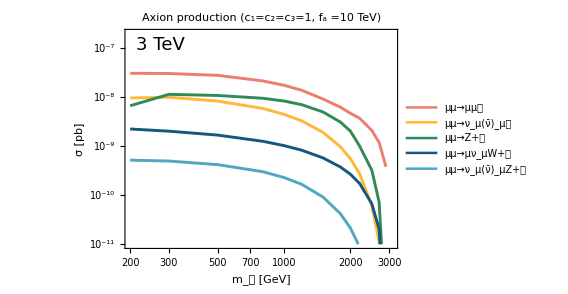

```mathematica
xsplot=ListLogLogPlot[{xsmumu2mumuaxdata,xsmumu2vmvmaxdata,xsmumu2Vaxdata,xswa2waxdata,xsww2zaxdata},Joined->True,PlotRange->{{2*10^2,3.1*10^3},{10^-11,2*10^-7}},PlotStyle->{{ColorData[24][1],Thickness[0.005]},{ColorData[24][2],Thickness[0.005]},{RGBColor[0.1875,0.54687,0.347656,1],Thickness[0.005]},{ColorData[24][7],Thickness[0.005]},{ColorData[24][5],Thickness[0.005]}},PlotLabel->Style["Axion production (c_1=c_2=c_3=1, f_a =10 TeV)",Black,18,FontFamily->"Times"],Frame->True,FrameTicks->{{tickll,Automatic},{Automatic,Automatic}},FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_(|01d44e) [GeV]",Black,18,FontFamily->"Times"],Style["σ [pb]",Black,18,FontFamily->"Times"]},PlotLegends->{Placed[LineLegend[{Style["μμ→μμ𝑎",Black,15,FontFamily->"Times"],Style["μμ→ν_μ(ν̄)_μ𝑎",Black,15,FontFamily->"Times"],Style["μμ→Z+𝑎",Black,15,FontFamily->"Times"],Style["μμ→μν_μW+𝑎",Black,15,FontFamily->"Times"],Style["μμ→ν_μ(ν̄)_μZ+𝑎",Black,15,FontFamily->"Times"]},LegendLayout->{"Row",2}],{{0.001,0.07},{0.0,0.3}}]},Epilog->{Text[Style["3 TeV",Black,18,FontFamily->"Times"],Scaled[{0.04,0.93}],Left,{1,0}]},AspectRatio->0.7,ImageSize->420]
```